```mathematica
h1[n_,x_]:=Simplify[
                                               Exp [x^2]*( D[ Exp[-(x-t)^2],{t,n} ] /. t->0 )
                                            ];
```

```mathematica
h1[13,z]
```

128 z (135135-540540 z^2+540540 z^4-205920 z^6+34320 z^8-2496 z^10+64 z^12)

```mathematica
(* OCCHIO alle tonde(), danno priorità alle operazioni presenti al loro interno *)
```

```mathematica
hermi[0,x_]=1;
hermi[1,x_]=2x;
hermi[n_Integer,x_]:= Expand[(2 x) (hermi[n-1,x] + 2 (n-1) hermi[n-2,x])];

primi7=MatrixForm[Table[hermi[i,x],{i,0,6}]]

ps[i_,j_]:= Integrate[ hermi[i,x] hermi[j,x] (-2 x Exp[-x^2]),{x,-Infinity,Infinity}];
check= Table[ ps[i,j] , {i,0,5} , {j,0,5}]//MatrixForm
```

(1
2 x
4 x+4 x^2
24 x^2+8 x^3
48 x^2+96 x^3+16 x^4
480 x^3+320 x^4+32 x^5
960 x^3+2880 x^4+960 x^5+64 x^6)

(0 | -2 √π | -4 √π | -12 √π | -144 √π | -840 √π
-2 √π | 0 | -12 √π | -72 √π | -264 √π | -2400 √π
-4 √π | -12 √π | -48 √π | -264 √π | -1968 √π | -13680 √π
-12 √π | -72 √π | -264 √π | -1440 √π | -11760 √π | -86880 √π
-144 √π | -264 √π | -1968 √π | -11760 √π | -74880 √π | -640800 √π
-840 √π | -2400 √π | -13680 √π | -86880 √π | -640800 √π | -5241600 √π)

```mathematica
eqh = y''[x] + (2  n+1 -x^2) y[x]==0 ;
solh[k_]=y[x]/.DSolve[eqh , y[x],x];
```

```mathematica
solh[5]=solh[5]/.{C[1]->0,C[2]->1}
```

ParabolicCylinderD[-6,ⅈ √2 x]

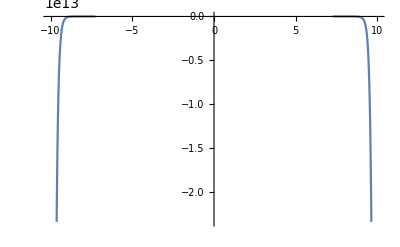

```mathematica
Plot[%145, {x,-10,10}]
```